# Least Squares Fitting—Polynomial

### Author

Eric W. Weisstein
March 15, 2009

This notebook downloaded from http://mathworld.wolfram.com/notebooks/Statistics/LeastSquaresFittingPolynomial.nb.

For more information, see Eric's MathWorld entry http://mathworld.wolfram.com/LeastSquaresFittingPolynomial.html.

©2009 Wolfram Research, Inc. except for portions noted otherwise

## Example

```mathematica
PolynomialFit[data_,n_]:=Module[{k,x,y,XT},
{x,y}=Transpose[data];
XT=Table[x^k,{k,0,n}];
Inverse[XT.Transpose[XT]].XT.y
]
```

```mathematica
data=Table[{x,-x^3+2x^2+5x+3}+0.001RandomReal[{0,1},2],{x,0,20}]
```

{{0.0000543862,3.00094},{1.00069,9.0002},{2.00096,13.0005},{3.0007,9.00015},{4.00091,-8.99978},{5.00089,-46.9996},{6.00048,-111.},{7.00027,-207.},{8.00025,-340.999},{9.00036,-518.999},{10.001,-746.999},{11.0003,-1031.},{12.0009,-1377.},{13.0001,-1791.},{14.0008,-2279.},{15.0003,-2847.},{16.0004,-3501.},{17.0004,-4247.},{18.0001,-5091.},{19.,-6039.},{20.0004,-7097.}}

```mathematica
fit=PolynomialFit[data,3]
```

{3.0031,4.98837,2.00404,-1.00015}

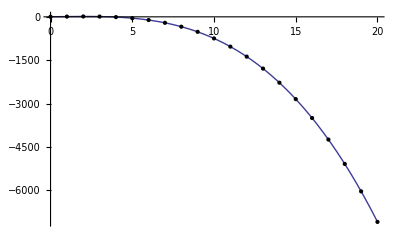

```mathematica
Plot[x^Range[0,3].fit,{x,0,20},Epilog->{Point[data]}]
```